# Exercises chapter 1 McE&B

A more extensive discussion and interpretation of all exercises can be found in the accompanying jupyter worksheet in html format, where I also provide step-by-step derivations. 
This worksheet just serves to show you how to do things in Mathematica.

Always erase any previous memory:

```mathematica
Clear["Global`*"]
```

## Exercise 1

See also 	 for a good piece of cobweb plot. However, for the sake of documentation I have made my own plot here (let me know if it breaks down):

```mathematica
ClearAll[CobwebPlot]
Options[CobwebPlot]=Join[{CobStyle->Automatic},Options[Graphics]];
CobwebPlot[f_,start_?NumericQ,n_,xrange:{xmin_,xmax_},opts:OptionsPattern[]]:=Module[{cob,x,g1,coor},cob=NestList[f,N[start],n];
coor=Partition[Riffle[cob,cob],2,1];
coor[[1,2]]=0;
cobstyle=OptionValue[CobwebPlot,CobStyle];
cobstyle=If[cobstyle===Automatic,Red,cobstyle];
g1=Graphics[{cobstyle,Line[coor]}];
Show[{Plot[{x,f[x]},{x,xmin,xmax},PlotStyle->{{Thin,Black},{Thick,Black}}],g1},FilterRules[{opts},Options[Graphics]]]]
```

And here an example. Rather than writing p wA / (p wA + (1-p) wB) we write the p as a # and then close off the expression with an ampersand ‘&’ so that mathematica knows this is our variable, rather than a parameter. 

We start from starting value 0.1, go for 10 iterations and the range of the x-axis is from 0 to 1. There are also some additional styling options you can explore for yourself

For a=-1.5:

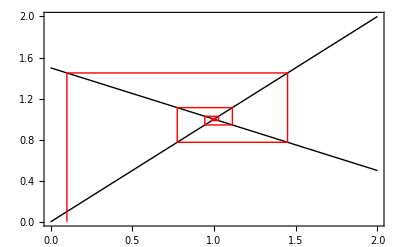

```mathematica
CobwebPlot[#+a(#-1)&/.a->-1.5,0.1,10,{0,2},PlotRange->{Automatic,Automatic},Frame->True,Axes->False,CobStyle->Red,PlotRangePadding->None]
```

For a=-2:

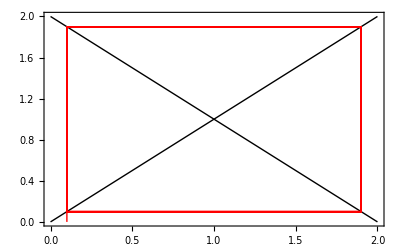

```mathematica
CobwebPlot[#+a(#-1)&/.a->-2,0.1,10,{0,2},PlotRange->{Automatic,Automatic},Frame->True,Axes->False,CobStyle->Red,PlotRangePadding->None]
```

For a=-2.5:

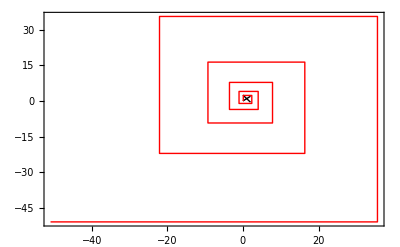

```mathematica
CobwebPlot[#+a(#-1)&/.a->-2.5,0.1,10,{0,2},PlotRange->{Automatic,Automatic},Frame->True,Axes->False,CobStyle->Red,PlotRangePadding->None]
```

## Exercise 2:

Specify the recursion:

```mathematica
pprime=p-m12 p+m21(1-p)
```

m21 (1-p)+p-m12 p

Solve for the equilibria

```mathematica
phat=Solve[pprime==p,p]//Flatten
```

{p→m21/(m12+m21)}

Now take the derivative

```mathematica
dpprimedp=D[pprime,p]/.p->phat
```

1-m12-m21

We can then even formally provide stability conditions, by feeding all our conditions into mathematica’s Reduce:

```mathematica
Reduce[{-1<dpprimedp<1,0<m12<1,0<m21<1}]
```

0<m21<1&&0<m12<1

Showing us that -1 < dp’/dp < 1 holds as long as 0<m12<1,0<m21<1.

## Exercise 3

See the mating table in the jupyter worksheet.

```mathematica
pprime3=p^2+2p(1-p)(1-e)
```

2 (1-e) (1-p) p+p^2

```mathematica
Δp3=pprime3-p//Simplify
```

(-1+2 e) (-1+p) p

## Exercise 4

We write the recursion from the mating table developed in the jupyter notebook:

```mathematica
pt1=(p^2 wAA+2p(1-p)(1/2)wAS)/(p^2 wAA+2p(1-p)wAS+(1-p)^2 wSS)
```

(p^2 wAA+(1-p) p wAS)/(p^2 wAA+2 (1-p) p wAS+(1-p)^2 wSS)

We then calculate the difference equation, simply by calculating p’ - p:

```mathematica
Δp=pt1-p//Simplify
```

-((-1+p) p (wAS-wSS+p (wAA-2 wAS+wSS)))/(2 p (wAS-wSS)+wSS+p^2 (wAA-2 wAS+wSS))

Solve for equilibria (i.e., where Δp == 0):

```mathematica
sol=Solve[Δp==0,p]
```

{{p→0},{p→1},{p→(-wAS+wSS)/(wAA-2 wAS+wSS)}}

Calculate stability of the equilibria

```mathematica
D[pt1,p]/.sol//Simplify
```

{wAS/wSS,wAS/wAA,(wAA wAS-2 wAA wSS+wAS wSS)/(wAS^2-wAA wSS)}

We can immediately see

```mathematica
wAS>wSS
```

```mathematica
wAS>wAA
```

## Exercise 5

```mathematica
pprime=p wAwet/(p wAwet + (1-p) wBwet)
```

(p wAwet)/(p wAwet+(1-p) wBwet)

```mathematica
pprimeprime =pprime wAdry/(pprime wAdry + (1-pprime) wBdry)//Simplify
```

(p wAdry wAwet)/(p wAdry wAwet+wBdry wBwet-p wBdry wBwet)

```mathematica
Δp=pprimeprime-p//Together//Simplify
```

-((-1+p) p (wAdry wAwet-wBdry wBwet))/(p wAdry wAwet+wBdry wBwet-p wBdry wBwet)

```mathematica
ex5sols=Solve[pprimeprime==p,p]//Simplify
```

{{p→0},{p→1}}

Indeed, only the equilibrium where A=1, (p=1) is completely stable, as its evaluated sign of the derivative is 0.2

```mathematica
D[pprimeprime,p]/.ex5sols/.{wAdry->1,wAwet->1,wBdry->0.2,wBwet->2}
```

{2.5,0.4}